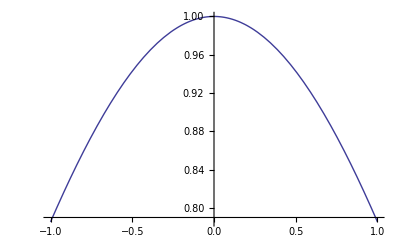

```mathematica
Needs["FunctionApproximations`"]
Plot[Cos[x*Pi/2]/(1-x^2),{x,-1,1}]
```

```mathematica
(MiniMaxApproximation[Cos[Pi*x/2]/(1-x^2),{x,{-0.999,0.999},3,0},PlotFlag->True&&PrintFlag->true&&MaxIterations->50])
```

{{-0.999,-0.723467,-4.36515×10^-15,0.723467,0.999},{0.997383+1.65984×10^-16 x-0.214077 x^2-1.48849×10^-16 x^3,0.00261658}}

```mathematica
MiniMaxApproximation[1/2 Erfc[-x/(√2)],{x,{0,5},4,5},Brake->{10,10}&&MaxIterations->500][[2,1]]
```

MiniMaxApproximation::conv: Warning: convergence was not complete.

(0.500006+0.258306 x+0.0131948 x^2+0.0067541 x^3+0.013347 x^4)/(1-0.28077 x+0.247371 x^2-0.0444257 x^3+0.0189689 x^4-0.00024807 x^5)

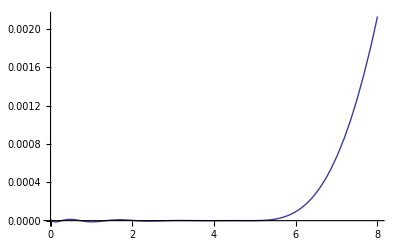

```mathematica
Plot[Log[%23/(1/2 Erfc[-x/(√2)])],{x,0,8} ,PlotRange->Full]
```

```mathematica
floom[y]
```

```mathematica
psi=HornerForm[MiniMaxApproximation[(1/2 Erfc[-x/(√2)]-1/2)/x,{x,{0.1,5},3,5},Bias->-0][[2,1]]*x]
```

(x (-664.282+x (211.052+(-54.6369-3.13535 x) x)))/(-1665.13+x (529.232+x (-414.991+x (80.874+x (-28.0145+1. x)))))

```mathematica
HornerForm[MiniMaxApproximation[(1/2 Erfc[-x/(√2)]-1/2)/x,{x,{0.05,5},4,5}][[2,1]]*x]
```

(x (-6738.03+x (2057.05+x (-551.013+(-30.5159-4.29621 x) x))))/(-16889.6+x (5153.98+x (-4185.16+x (762.029+x (-271.851+1. x)))))

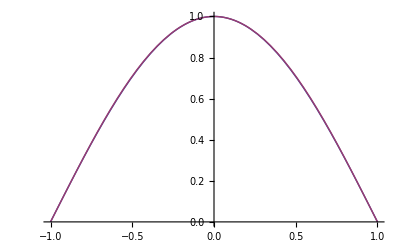

```mathematica
Plot[{Cos[x*Pi/2],1+(Pi/4-2)*x^2+(1-Pi/4)*x^4},{x,-1,1}]
```

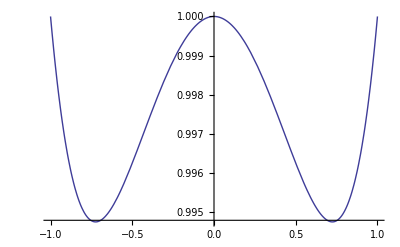

```mathematica
Plot[Cos[x*Pi/2]/(1+(Pi/4-2)*x^2+(1-Pi/4)*x^4),{x,-1,1}]
```

```mathematica
N[HornerForm[(1+(Pi/4-2)*x^2+(1-Pi/4)*x^4),x]]
```

1.+x^2 (-1.2146+0.214602 x^2)

1.+x^2 (-1.2146+0.214602 x^2)

1.+x^2 (-1.2146+0.214602 x^2)

```mathematica
Log10[0.994^2]*10
```

-0.0522723

```mathematica
-0.0261361560268669
```

-0.0261362

```mathematica
g[x_]:=Cos[Pi*x/2]
g[1]
```

```mathematica
0
gd[x_]=D[g[x],x]
```

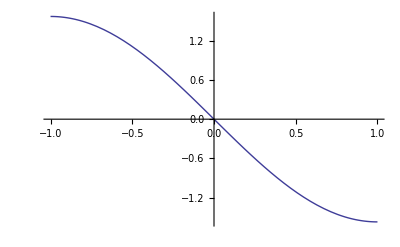

```mathematica
Plot[gd[x],{x,-1,1}]
```

```mathematica
N[HornerForm[Simplify[InterpolatingPolynomial[{{-1,g[-1],gd[-1]},{-2/3,g[-2/3],gd[-2/3]},{0,g[0],gd[0]},{2/3,g[2/3],gd[2/3]},{1,g[1],gd[1]}},x]]] ]
```

1.+x^2 (-1.2337+x^2 (0.253639+x^2 (-0.0207919+0.000848933 x^2)))

```mathematica
N[HornerForm[Simplify[InterpolatingPolynomial[{{-1,g[-1],gd[-1]},{0,g[0],gd[0]},{1,g[1],gd[1]}},x]]] ]
```

1.+x^2 (-1.2146+0.214602 x^2)